## Generating 5-fold symmetry axis on 2D surface

n= 1

```mathematica
a1 = Cos[2π/5];
b1 = Cos[π/5];
c1 = Sin[2π/5];
d1 = Sin[4π/5];
vertices={{a1,-c1}, {1,0}, {a1,c1}, {-b1,d1}, {-b1,-d1}};
transv1 = {{a1+1,-c1}, {1+1,0}, {a1+1,c1}, {-b1+1,d1}, {-b1+1,-d1}};
```

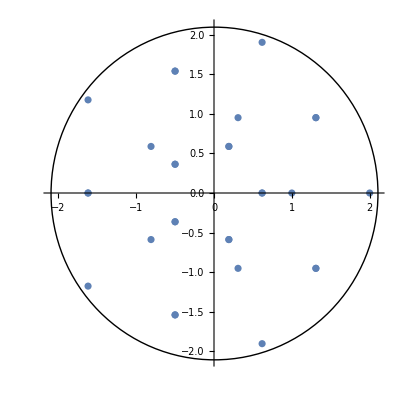

```mathematica
rotv1 = RotationTransform[2π/5, {0,0}] /@ # &@transv1;
rotv2 = RotationTransform[2π/5, {0,0}] /@ # &@rotv1;
rotv3 = RotationTransform[2π/5, {0,0}] /@ # &@rotv2;
rotv4 = RotationTransform[2π/5, {0,0}] /@ # &@rotv3;
n1point = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4], AspectRatio->1];
circle = Graphics[Circle[{0, 0}, 2.1]];
n1 = Show[n1point, circle, PlotRange-> All]
```

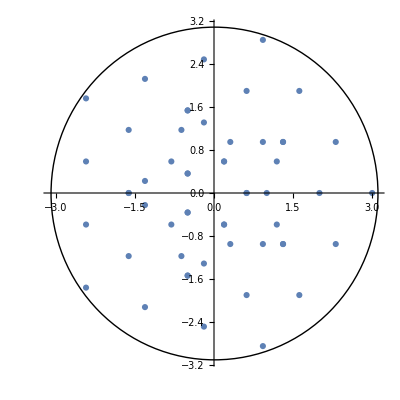

-Graphics-

```mathematica
a1 = Cos[2π/5];
b1 = Cos[π/5];
c1 = Sin[2π/5];
d1 = Sin[4π/5];
vertices={{a1,-c1}, {1,0}, {a1,c1}, {-b1,d1}, {-b1,-d1}};
transv1 = {{a1+1,-c1}, {1+1,0}, {a1+1,c1}, {-b1+1,d1}, {-b1+1,-d1}};
rotv1 = RotationTransform[2π/5, {0,0}] /@ # &@transv1;
rotv2 = RotationTransform[2π/5, {0,0}] /@ # &@rotv1;
rotv3 = RotationTransform[2π/5, {0,0}] /@ # &@rotv2;
rotv4 = RotationTransform[2π/5, {0,0}] /@ # &@rotv3;
transv2 = {{a1+2,-c1}, {1+2,0}, {a1+2,c1}, {-b1+2,d1}, {-b1+2,-d1}};
rotv5 = RotationTransform[2π/5, {0,0}] /@ # &@transv2;
rotv6 = RotationTransform[2π/5, {0,0}] /@ # &@rotv5;
rotv7 = RotationTransform[2π/5, {0,0}] /@ # &@rotv6;
rotv8 = RotationTransform[2π/5, {0,0}] /@ # &@rotv7;
n2point = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4, transv2, rotv5, rotv6, rotv7, rotv8], AspectRatio->1];
circle2 = Graphics[Circle[{0, 0}, 3.1]];
n2 = Show[n2point, circle2, PlotRange-> All]
```

## Loading data

import data as string:

```mathematica
data =Import[URLDownload["https://files.rcsb.org/download/3J3I.pdb1.gz"],"String"];
```

replace negative signs(-) with spaces to separate columns:

```mathematica
spaced  = StringReplace[data,"-"-> " -"];
```

export modified file to directory as text:

```mathematica
Export["/Users/Jihyeon/Desktop/3J3I_spaced.txt",spaced];
```

open modified file:

```mathematica
str = OpenRead["/Users/Jihyeon/Desktop/1JS9_spaced.txt"];
```

Read data starting from row 180:

```mathematica
Do[Read[str,"String"],181]
```

```mathematica
Read[str,"String"]
```

ATOM      1  N   LYS A  41      71.779  -11.151  76.910  1.00168.69           N

read the list as words

```mathematica
fullrecord=ReadList[str,"Word", RecordLists->True];
```

split the list when consecutive first letter appears:

```mathematica
splitted = Split[fullrecord,First[#1]===First[#2]&];
```

remove unnecessary rows:

```mathematica
removed = DeleteCases[splitted,x_/;First[First[x]]== "TER"];
removed = DeleteCases[removed,x_/;First[First[x]]== "HETATM"];
removed = DeleteCases[removed,x_/;First[First[x]]== "MODEL"];
removed = DeleteCases[removed,x_/;First[First[x]]== "ENDMDL"];
removed = DeleteCases[removed,x_/;First[First[x]]== "MASTER"];
removed = DeleteCases[removed,x_/;First[First[x]]== "END"];
```

```mathematica
Dimensions[removed]
```

{180}

## Calculating center of mass

### extracting coordinates

only extract atom data and coordinates:

```mathematica
atom =   removed⟦All,All, -1⟧;
```

replace atoms with its atomic mass:

```mathematica
mass = atom/.{"N"->14.00, "C" -> 12.01, "O" -> 15.99, "S" -> 32.06};
```

extract x,y,z coordinates:

```mathematica
xcoor =  ToExpression[removed⟦All,All, 7⟧]
```

{1}
 |  |  |  |

```mathematica
ycoor =  ToExpression[removed⟦All,All, 8⟧]
```

{1}
 |  |  |  |

```mathematica
zcoor =  ToExpression[removed⟦All,All, 9⟧]
```

{1}
 |  |  |  |

```mathematica
chain = removed⟦All,All, 5⟧
```

{1}
 |  |  |  |

### Calculation

equation for calculating center of mass:

```mathematica
calcx[mass_,xcoor_] :=Sum[mass[[i]]* xcoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
xset = MapThread[calcx, {mass, xcoor}];
```

```mathematica
calcy[mass_,ycoor_] :=Sum[mass[[i]]* ycoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
yset = MapThread[calcy, {mass, ycoor}];
```

```mathematica
calcz[mass_,zcoor_] :=Sum[mass[[i]]* zcoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
zset = MapThread[calcz, {mass, zcoor}];
```

put all x, y, z center of mass coordinates together:

```mathematica
totcentercoor[xset_,yset_,zset_] :=List[xset, yset, zset]
centercoor = MapThread[totcentercoor, {xset, yset, zset}];
```

## Graphing points in 3D

```mathematica
flatchain = Flatten@chain;
```

```mathematica
x = Flatten[xcoor];
y = Flatten[ycoor];
z = Flatten[zcoor];
```

Put all x,y,z coordinates together:

```mathematica
totcoor[x_,y_,z_] :=List[x, y, z]
allcoor = MapThread[totcoor, {x, y, z}];
```

Match color with each protein:

```mathematica
colorlist = ToExpression[flatchain/.{"A"-> "Blue", "B" -> "Pink", "C" -> "Green", "D" -> "Red"}];
```

```mathematica
Graphics3D[{Point[allcoor,VertexColors->colorlist]}, Lighting->Automatic, Boxed->False]
```

-Graphics3D-

Match color with chain type for each center of mass coordinates:

```mathematica
chaintype = First /@ chain;
```

```mathematica
colorlist2 = ToExpression[chaintype/.{"A"-> "Blue", "B" -> "Pink", "C" -> "Green", "D" -> "Red"}];
```

Generate point cloud with center of mass:

```mathematica
Graphics3D[{PointSize[0.02],Point[centercoor,VertexColors->colorlist2]}]
```

-Graphics3D-

Create surface mesh to see general structure:

```mathematica
ListSurfacePlot3D[centercoor, BoxRatios->{1, 1, 1}]
```

-Graphics3D-

## Tiling

### Generate mesh

```mathematica
cm =RegionBoundary@DelaunayMesh@centercoor
```

-Graphics3D-

### Generate tiling

```mathematica
normal[Polygon[{p1_,p2_,p3_}]]:=Normalize@Cross[p1-p2,p1-p3]
```

```mathematica
delaunaymesh = DelaunayMesh@centercoor;
trianglecomponents = MeshPrimitives[RegionBoundary@delaunaymesh,2];
```

```mathematica
normals=normal/@trianglecomponents;
```

```mathematica
rounded = Round[normals,0.1];
```

```mathematica
tally = Tally[rounded];
```

```mathematica
pent = GatherBy[tally,Last][[2]];
quad =  GatherBy[tally,Last][[3]];
tri =  GatherBy[tally,Last][[1]];
```

```mathematica
pentcoor = First /@ pent;
quadcoor = First /@ quad;
tricoor = First /@ tri;
```

```mathematica
value1 = Flatten /@ Map[Position[ rounded, #]&, pentcoor];
value2 = Flatten /@ Map[Position[ rounded, #]&, quadcoor];
value3 = Flatten /@ Map[Position[ rounded, #]&, tricoor];
```

```mathematica
coors1 = Map[Part[trianglecomponents,#] &, value1];
coors2 = Map[Part[trianglecomponents,#] &, value2];
coors3 = Map[Part[trianglecomponents,#] &, value3];
```

```mathematica
flat = Flatten[Map[ReplaceAll[Polygon->List][#] &, coors3],2];
subset = Map[Subsets[#, {2}]&,flat];
```

```mathematica
distance = Round[Apply[EuclideanDistance, subset, {2}],0.1];
equilateral[{x_,y_,z_}]:=(If[x==y==z,Return[1]])
```

```mathematica
positions = Flatten[ Position[equilateral /@ distance,1],1];
```

```mathematica
center = Map[Part[coors3,#] &, positions];
```

```mathematica
graphed = Graphics3D[{White, Point[Mean/@ pentcoorext],Blue,EdgeForm[],coors1,Pink,EdgeForm[],coors2, Yellow,EdgeForm[{Thick, Black}], coors3, Green, EdgeForm[], center}, Lighting->Automatic, Boxed->False]
```

-Graphics3D-

I think you can get the unit cell “triangles” as follows:

```mathematica
DelaunayMesh[Mean/@ pentcoorext]
```

```mathematica
MeshPrimitives[DelaunayMesh[Mean/@ pentcoorext],2]
```

{Polygon[{{113.692,-15.2294,-21.889},{-70.033,-90.8344,-21.9394},{70.033,90.8344,21.9394}}],Polygon[{{-70.033,-90.8344,-21.9394},{113.692,-15.2294,-21.889},{-43.3023,-56.1623,92.777}}],Polygon[{{113.692,-15.2294,-21.889},{70.033,90.8344,21.9394},{-43.3023,-56.1623,92.777}}],Polygon[{{70.033,90.8344,21.9394},{-70.033,-90.8344,-21.9394},{-43.3023,-56.1623,92.777}}],Polygon[{{70.033,90.8344,21.9394},{-26.9946,65.5365,92.8069},{70.2482,-9.43195,92.8094}}],Polygon[{{-26.9946,65.5365,92.8069},{70.033,90.8344,21.9394},{-43.3023,-56.1623,92.777}}],Polygon[{{70.033,90.8344,21.9394},{70.2482,-9.43195,92.8094},{-43.3023,-56.1623,92.777}}],Polygon[{{70.2482,-9.43195,92.8094},{-26.9946,65.5365,92.8069},{-43.3023,-56.1623,92.777}}],Polygon[{{70.033,90.8344,21.9394},{-26.9946,65.5365,92.8069},{-113.692,15.2294,21.889}}],Polygon[{{-26.9946,65.5365,92.8069},{70.033,90.8344,21.9394},{-43.6466,106.078,-21.891}}],Polygon[{{70.033,90.8344,21.9394},{-113.692,15.2294,21.889},{-43.6466,106.078,-21.891}}],Polygon[{{-113.692,15.2294,21.889},{-26.9946,65.5365,92.8069},{-43.6466,106.078,-21.891}}],Polygon[{{-70.2458,9.43579,-92.8081},{113.692,-15.2294,-21.889},{26.9946,-65.5365,-92.8069}}],Polygon[{{113.692,-15.2294,-21.889},{-70.2458,9.43579,-92.8081},{-70.033,-90.8344,-21.9394}}],Polygon[{{-70.2458,9.43579,-92.8081},{26.9946,-65.5365,-92.8069},{-70.033,-90.8344,-21.9394}}],Polygon[{{26.9946,-65.5365,-92.8069},{113.692,-15.2294,-21.889},{-70.033,-90.8344,-21.9394}}],Polygon[{{26.9946,-65.5365,-92.8069},{113.692,-15.2294,-21.889},{43.6466,-106.078,21.891}}],Polygon[{{26.9946,-65.5365,-92.8069},{43.6466,-106.078,21.891},{-70.033,-90.8344,-21.9394}}],Polygon[{{43.6466,-106.078,21.891},{113.692,-15.2294,-21.889},{-70.033,-90.8344,-21.9394}}],Polygon[{{-26.9946,65.5365,92.8069},{-113.692,15.2294,21.889},{-43.3023,-56.1623,92.777}}],Polygon[{{-113.692,15.2294,21.889},{70.033,90.8344,21.9394},{-43.3023,-56.1623,92.777}}],Polygon[{{-70.2458,9.43579,-92.8081},{43.3023,56.1623,-92.777},{26.9946,-65.5365,-92.8069}}],Polygon[{{43.3023,56.1623,-92.777},{-70.2458,9.43579,-92.8081},{113.692,-15.2294,-21.889}}],Polygon[{{26.9946,-65.5365,-92.8069},{43.3023,56.1623,-92.777},{113.692,-15.2294,-21.889}}],Polygon[{{113.692,-15.2294,-21.889},{43.3023,56.1623,-92.777},{-43.6466,106.078,-21.891}}],Polygon[{{43.3023,56.1623,-92.777},{-70.2458,9.43579,-92.8081},{-43.6466,106.078,-21.891}}],Polygon[{{-70.2458,9.43579,-92.8081},{113.692,-15.2294,-21.889},{-43.6466,106.078,-21.891}}],Polygon[{{70.033,90.8344,21.9394},{-70.033,-90.8344,-21.9394},{-113.692,15.2294,21.889}}],Polygon[{{-113.692,15.2294,21.889},{-70.033,-90.8344,-21.9394},{-43.3023,-56.1623,92.777}}],Polygon[{{70.033,90.8344,21.9394},{113.692,-15.2294,-21.889},{43.3023,56.1623,-92.777}}],Polygon[{{113.692,-15.2294,-21.889},{70.033,90.8344,21.9394},{-43.6466,106.078,-21.891}}],Polygon[{{70.033,90.8344,21.9394},{43.3023,56.1623,-92.777},{-43.6466,106.078,-21.891}}],Polygon[{{-70.033,-90.8344,-21.9394},{-113.692,15.2294,21.889},{-43.6466,106.078,-21.891}}],Polygon[{{70.033,90.8344,21.9394},{-70.033,-90.8344,-21.9394},{-43.6466,106.078,-21.891}}],Polygon[{{-70.2458,9.43579,-92.8081},{-70.033,-90.8344,-21.9394},{-113.692,15.2294,21.889}}],Polygon[{{-70.033,-90.8344,-21.9394},{-70.2458,9.43579,-92.8081},{-43.6466,106.078,-21.891}}],Polygon[{{-70.2458,9.43579,-92.8081},{-113.692,15.2294,21.889},{-43.6466,106.078,-21.891}}],Polygon[{{-70.033,-90.8344,-21.9394},{113.692,-15.2294,-21.889},{-43.6466,106.078,-21.891}}],Polygon[{{-70.033,-90.8344,-21.9394},{43.6466,-106.078,21.891},{-43.3023,-56.1623,92.777}}],Polygon[{{43.6466,-106.078,21.891},{113.692,-15.2294,-21.889},{-43.3023,-56.1623,92.777}}],Polygon[{{70.2482,-9.43195,92.8094},{113.692,-15.2294,-21.889},{70.033,90.8344,21.9394}}],Polygon[{{113.692,-15.2294,-21.889},{70.2482,-9.43195,92.8094},{-43.3023,-56.1623,92.777}}],Polygon[{{43.6466,-106.078,21.891},{113.692,-15.2294,-21.889},{70.2482,-9.43195,92.8094}}],Polygon[{{43.6466,-106.078,21.891},{70.2482,-9.43195,92.8094},{-43.3023,-56.1623,92.777}}]}

```mathematica
(Mean/@ pentcoorext)/120
```

{{0.94743,-0.126911,-0.182408},{0.360852,0.468019,-0.773141},{0.224955,-0.546138,-0.773391},{0.583608,0.756954,0.182828},{0.363722,-0.883986,0.182425},{-0.360852,-0.468019,0.773142},{-0.363722,0.883986,-0.182425},{0.585402,-0.0785996,0.773412},{-0.224955,0.546138,0.773391},{-0.583608,-0.756954,-0.182828},{-0.94743,0.126911,0.182409},{-0.585382,0.0786316,-0.773401}}

#### Projecting onto plane

```mathematica
extracted[{Polygon[{r1_,r2_,r3_}],Polygon[{t1_,t2_,t3_}],Polygon[{y1_,y2_,y3_}]}]:= List[{r1,r2,r3,t1,t2,t3,y1,y2,y3}]
pentcoorext = DeleteDuplicates/@Flatten[extracted /@ coors1,1];
path1 = Last /@ FindShortestTour /@ pentcoorext;
pentfinal =  Map[Take[#,5]&,MapThread[Part, {pentcoorext,path1}]];
```

```mathematica
extracted2[{Polygon[{r1_,r2_,r3_}],Polygon[{t1_,t2_,t3_}]}]:= List[{r1,r2,r3,t1,t2,t3}]
quadextract = DeleteDuplicates/@Flatten[extracted2 /@ coors2,1];
path2 = Last /@ FindShortestTour /@ quadextract;
quadfinal =  Map[Take[#,4]&,MapThread[Part, {quadextract,path2}]];
```

```mathematica
extracted3[{Polygon[{r1_,r2_,r3_}]}]:= List[{r1,r2,r3}]
triextract = DeleteDuplicates/@Flatten[extracted3 /@ coors3,1];
path3 = Last /@ FindShortestTour /@ triextract;
trifinal =  Map[Take[#,3]&,MapThread[Part, {triextract,path3}]];
```

```mathematica
pentcenter = Mean/@ pentcoorext
```

{{113.692,-15.2294,-21.889},{43.3023,56.1623,-92.777},{26.9946,-65.5365,-92.8069},{70.033,90.8344,21.9394},{43.6466,-106.078,21.891},{-43.3023,-56.1623,92.777},{-43.6466,106.078,-21.891},{70.2482,-9.43195,92.8094},{-26.9946,65.5365,92.8069},{-70.033,-90.8344,-21.9394},{-113.692,15.2294,21.889},{-70.2458,9.43579,-92.8081}}

```mathematica
projector[projectingPoint_]:=Module[{a,b,c,d,nv,k},
{a,b,c}=Flatten[center[[9]]/.Polygon->List,2];
nv=Cross[b-a,c-a];
d=-nv.a;
k=(-d-nv.projectingPoint)/Norm[nv]^2;
projectingPoint+k*nv
]&;
```

```mathematica
object = 
Graphics3D[{
Polygon/@ Map[projector, Part[pentfinal,{1,2,3}],{2}],
center[[9]],
Polygon/@Map[projector,Part[quadfinal,{1,2,8}],{2}],
Polygon/@Map[projector,Part[trifinal,{12,4,3,45,64,69}],{2}],
 Boxed->False
}]
```

-Graphics3D-

```mathematica
Show[object,ViewPoint->{1.3,-2.4,2.}, Boxed->False, Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
{u,v,w}=center[[9,1,1]]
```

{{93.1707,-19.9469,-65.4244},{56.675,-27.5742,-96.8846},{72.408,17.8005,-88.3133}}

```mathematica
b=Orthogonalize[{v-u,w-u,Cross[v-u,w-u]}]
```

{{-0.748112,-0.15635,-0.64489},{-0.0595271,0.98374,-0.169447},{0.660897,-0.088377,-0.745254}}

```mathematica
i=Inverse[b]
```

{{-0.748112,-0.0595271,0.660897},{-0.15635,0.98374,-0.088377},{-0.64489,-0.169447,-0.745254}}

```mathematica
Planarize[x_,{u_,v_,w_}]:=x.Inverse[Orthogonalize[{v-u,w-u,Cross[v-u,w-u]}]]
```

orthogonalization:

```mathematica
pentproj = Map[projector, Part[pentfinal,{1,2,3}],{2}];
triproj = center[[9,1,1]];
quadproj = Map[projector,Part[quadfinal,{1,2,8}],{2}];
backproj = Map[projector,Part[trifinal,{12,4,3,45,64,69}],{2}];
```

```mathematica
pentextcoors = Map[Planarize[#,center[[9,1,1]]]&, pentproj ];
triextcoors = Map[Planarize[#,center[[9,1,1]]]&, triproj ];
quadextcoors =Map[Planarize[#,center[[9,1,1]]]&, quadproj ];
backextcoors = Map[Planarize[#,center[[9,1,1]]]&, backproj ];
```

```mathematica
map[x_]:= Map[Drop[#,-1]&,x]
```

```mathematica
pentflat=Polygon/@ map/@pentextcoors;
triflat=Polygon@Map[Drop[#,-1]&,triextcoors];
quadflat=Polygon/@map/@quadextcoors;
backflat = Polygon /@ map /@ backextcoors;
```

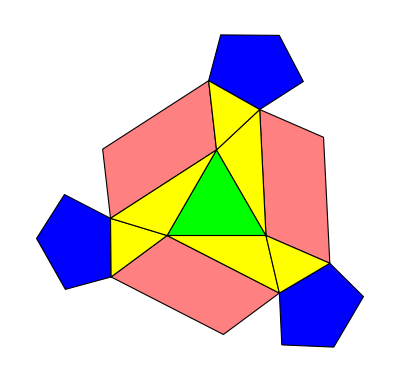

```mathematica
Graphics[{Tooltip[ {EdgeForm[{Thick,Black}],Blue,pentflat},ImageResize[Import[pentimg],{150}]],Tooltip[{EdgeForm[{Thick,Black}],Green,triflat},"ChainB"],Tooltip[ {EdgeForm[{Thick,Black}],Pink,quadflat},"ChainB"],Tooltip[ {EdgeForm[{Thick,Black}],Yellow,backflat},"ChainA"]}]
```

```mathematica
pentimg = "/Users/Jihyeon/Desktop/pent.jpg";
ImageResize[Import[pentimg],{150}]
```

-Graphics-